```mathematica
SetDirectory[NotebookDirectory[]];
```

## 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-((2857-(5033/9)Nf+(325/27) Nf^2)/128); (*for Nc=3 only*)
β3[Nf_]=((-1)/256)((149753/6+3564 Zeta[3])-(1078361/162+(6508/27) Zeta[3])Nf+(50065/162+(6472/81)Zeta[3])Nf^2+(1093/729) Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=(1/16)(202/3-(20/9)Nf);(*for Nc=3 only*)
γ2[Nf_]=(1/64)(1249+(-(2216/27)-(160/3) Zeta[3])Nf-(140/81) Nf^2);(*for Nc=3 only*)
γ3[Nf_]=(1/256)(4603055/162+(135680/27) Zeta[3]-8800Zeta[5]+(-(91723/27)-(34192/9) Zeta[3]+880 Zeta[4]+(18400/9)Zeta[5])Nf+(5242/243+(800/9) Zeta[3]-(160/3)Zeta[4])Nf^2+(-(332/243)+(64/27) Zeta[3])Nf^3);

b0[Nf_]=-((8β0[Nf])/(2(4π)^2));
b1[Nf_]=-((32 β1[Nf])/(2(4π)^2));

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=(-1)/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-( β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+(1/(β0[Nf]^7 t^4))( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

## Functions

```mathematica
R=20000;
Mc=1.4691897661033038;
Mb=4.882;
kfinal={0.6856700331366409,-0.31661256911352553};(*100k run*)
kfinalu={0.9065399936425322,-0.36858869824209667};
kfinall={0.4648000726307495,-0.2646364399849544};
αcont={0.5129548374487685,0.002435119807500435};(*10k run*)
σcont={0.16999653850906107,0.000838106749908169};
ccont={-0.1611740456186636,0.002474788649682089};
conv=0.197327;
ReVsbVac=8/10;
```

```mathematica
ReV[r_,mD_,α_,σ_,c_]:=c-α mD-α Exp[-mD r]/r+(2 σ)/mD-(ⅇ^(-mD r) (2+mD r) σ)/mD;
ImVc[r_,mD_,α_,T_]:=T α Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[mD r z]),{z,0,∞},MaxRecursion->20]];
ImVs[r_,mD_,σ_,T_]:=1/4 mD √π r^3 T σ MeijerG[{{-1/2,-1/2},{}},{{1/2,1/2},{-3/2,-1}},(mD^2 r^2)/4];
```

### Self energies

```mathematica
mDcalmu[T_,μ_,c_,d_]:=SetPrecision[Re[Sqrt[Nc/3+nF/6+nF/(2 π^2)(μ/3)^2/T^2]g4[2π √(T^2+μ^2/π^2)]T+1/(4π)Nc g4[2π √(T^2+μ^2/π^2)]^2 T Log[Sqrt[Nc/3+nF/6]/g4[2π √(T^2+μ^2/π^2)]]+c g4[2π √(T^2+μ^2/π^2)]^2 T+d g4[2π √(T^2+μ^2/π^2)]^3 T ],30];
```

```mathematica
Πper[θ_,ϕ_,β_,mD_,u_]:=SetPrecision[mD^2/2((2-2 u^2-u^4 Sin[θ]^2 Cos[ϕ-β]^2(1-Cos[ϕ-β]^2 Sin[θ]^2))/((1-u^2+u^2 Cos[ϕ-β]^2 Sin[θ]^2)^2)-((2+u^2-u^2 Sin[θ]^2 Cos[ϕ-β]^2)(1-u^2)u Cos[ϕ-β]Sin[θ])/(2(1-u^2+u^2 Cos[ϕ-β]^2 Sin[θ]^2)^(5/2))Log[(u Cos[ϕ-β] Sin[θ]+√(1-u^2+u^2 Cos[ϕ-β]^2 Sin[θ]^2))/(u Cos[ϕ-β]Sin[θ]-√(1-u^2+u^2 Cos[ϕ-β]^2 Sin[θ]^2))]),30];
```

## Plot potentials

```mathematica
uscan=Join[Table[i,{i,1/10,9/10,1/10}],{99/100}]
```

{1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,99/100}

```mathematica
Block[{data},Do[data=ToExpression[Import["vel_pot_perp/ReVsu"<>ToString[Round[100uscan[[n]]]]<>".dat"]];data=Append[data,{20000,data[[-1,2]]}];ReVsu[n]=Interpolation[data,InterpolationOrder->1],{n,Length[uscan]}]];
```

```mathematica
Block[{data},Do[data=ToExpression[Import["vel_pot_perp/ReVcu"<>ToString[Round[100uscan[[n]]]]<>".dat"]];data=Append[data,{20000,data[[-1,2]]}];ReVcu[n]=Interpolation[data,InterpolationOrder->1],{n,Length[uscan]}]];
```

```mathematica
Block[{data},Do[data=ToExpression[Import["vel_pot_perp/ImVcu"<>ToString[Round[100uscan[[n]]]]<>".dat"]];data=Append[data,{20000,data[[-1,2]]}];
data=Transpose[{data[[All,1]],EstimatedBackground[data[[All,2]]]}];ImVcu[n]=Interpolation[data,InterpolationOrder->1],{n,Length[uscan]}]];
```

```mathematica
Block[{data},Do[data=ToExpression[Import["vel_pot/ImVsu"<>ToString[Round[100uscan[[n]]]]<>".dat"]];data=Append[data,{20000,data[[-1,2]]}];ImVsu[n]=Interpolation[data,InterpolationOrder->1],{n,Length[uscan]}]];
```

```mathematica
uSetS={"1/10","2/10","3/10","4/10","5/10","6/10","7/10","8/10","9/10","99/100","Vac"};
```

```mathematica
mD1=mDcalmu[155/1000,0,kfinal[[1]],kfinal[[2]]]
```

0.207411256204937832769985561754

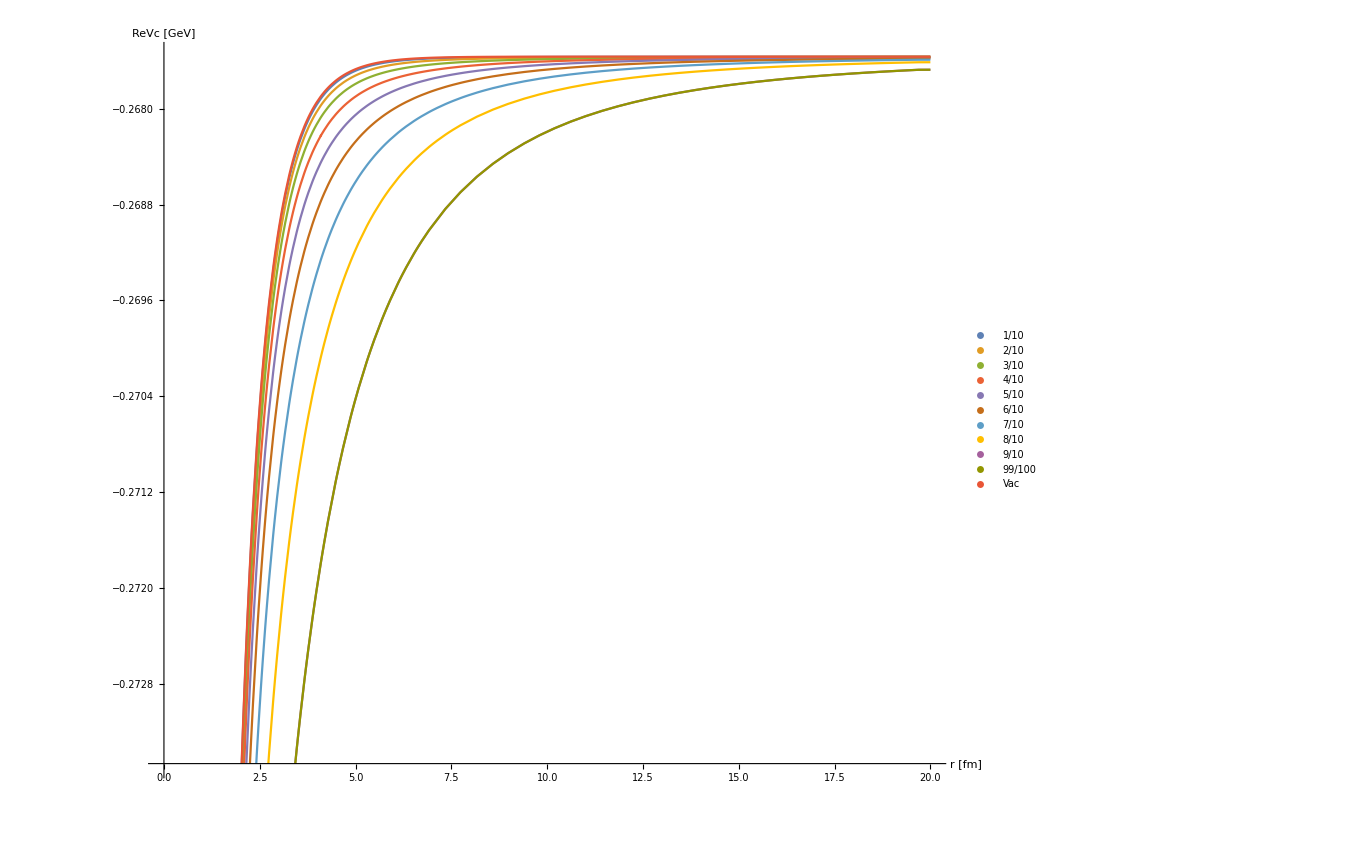

```mathematica
Plot[{ReVcu[1][r/0.197],ReVcu[2][r/0.197],ReVcu[3][r/0.197],ReVcu[4][r/0.197],ReVcu[5][r/0.197],ReVcu[6][r/0.197],ReVcu[7][r/0.197],ReVcu[8][r/0.197],ReVcu[9][r/0.197],ReVcu[9][r/0.197],ReV[r/0.197,mD1,αcont[[1]],0,ccont[[1]]]},{r,0,20},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ReVc [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.7,0.2}],BaseStyle->{FontSize->14}]
```

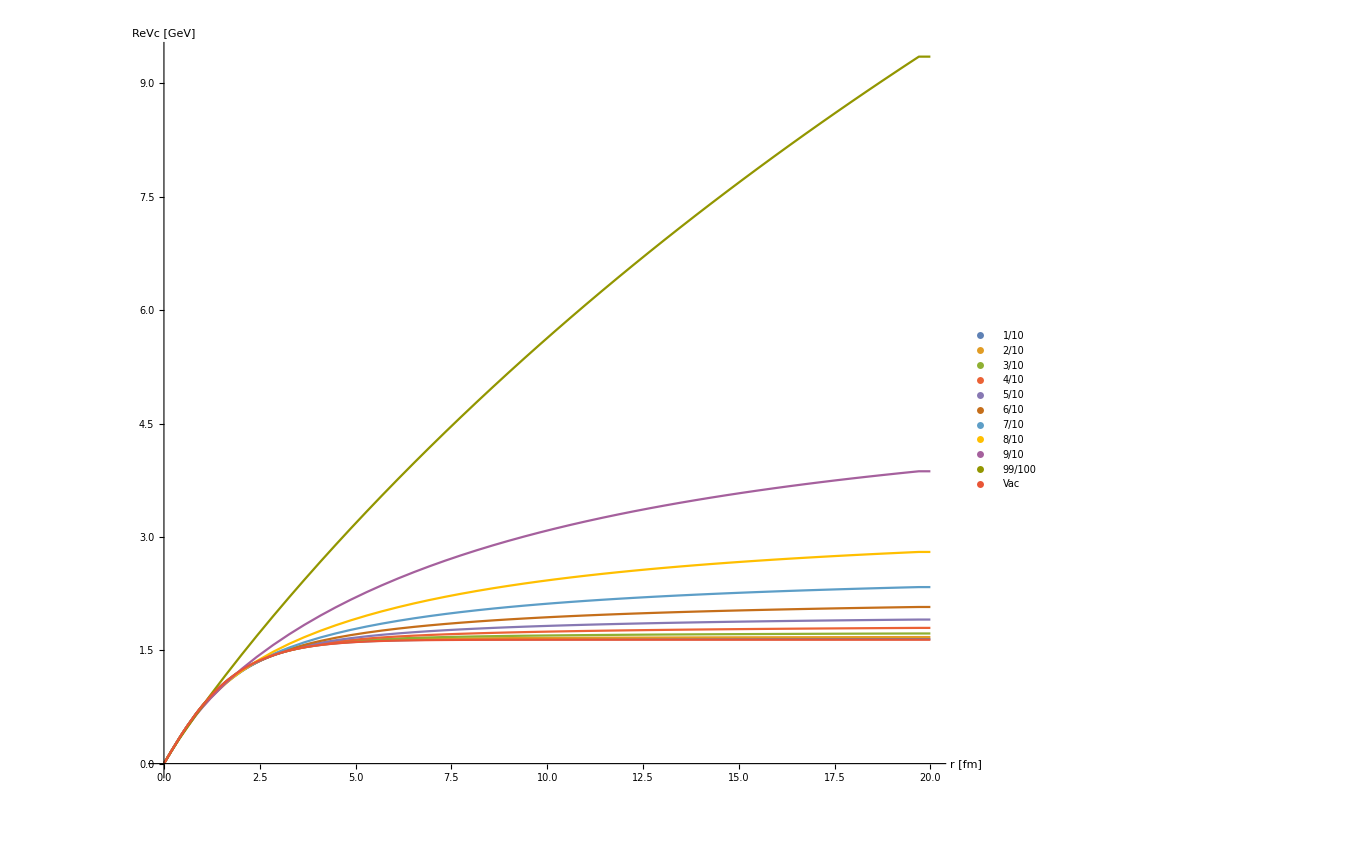

```mathematica
Plot[{ReVsu[1][r/0.197],ReVsu[2][r/0.197],ReVsu[3][r/0.197],ReVsu[4][r/0.197],ReVsu[5][r/0.197],ReVsu[6][r/0.197],ReVsu[7][r/0.197],ReVsu[8][r/0.197],ReVsu[9][r/0.197],ReVsu[10][r/0.197],ReV[r/0.197,mD1,0,σcont[[1]],0]},{r,0,20},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ReVc [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.7,0.2}],BaseStyle->{FontSize->14},PlotRange->All]
```

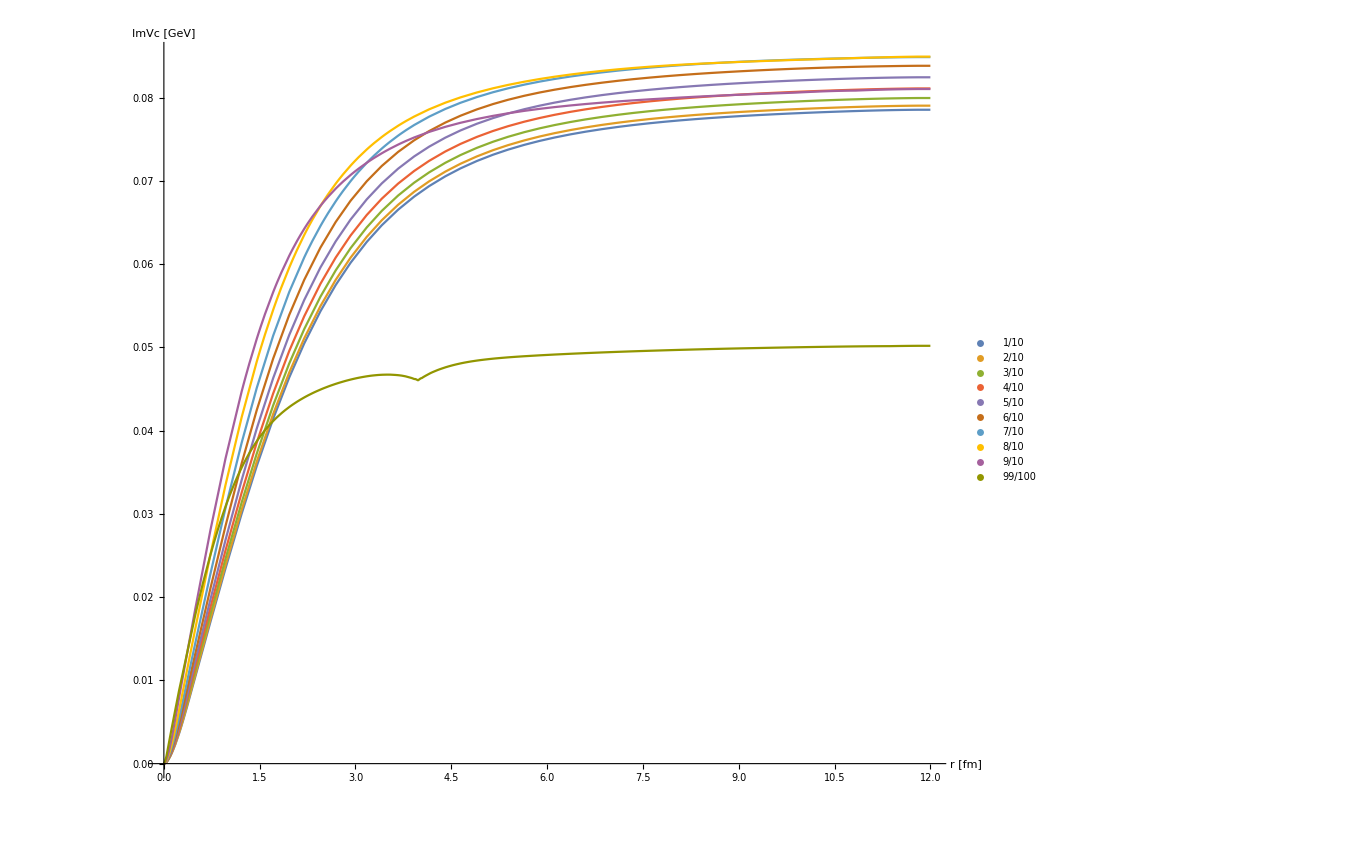

```mathematica
Plot[{Re[ImVcu[1][r/0.197]],Re[ImVcu[2][r/0.197]],Re[ImVcu[3][r/0.197]],Re[ImVcu[4][r/0.197]],Re[ImVcu[5][r/0.197]],Re[ImVcu[6][r/0.197]],Re[ImVcu[7][r/0.197]],Re[ImVcu[8][r/0.197]],Re[ImVcu[9][r/0.197]],Re[ImVcu[10][r/0.197]]},{r,1/1000,12},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVc [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.8,0.3}],BaseStyle->{FontSize->14},PlotRange->All]
```

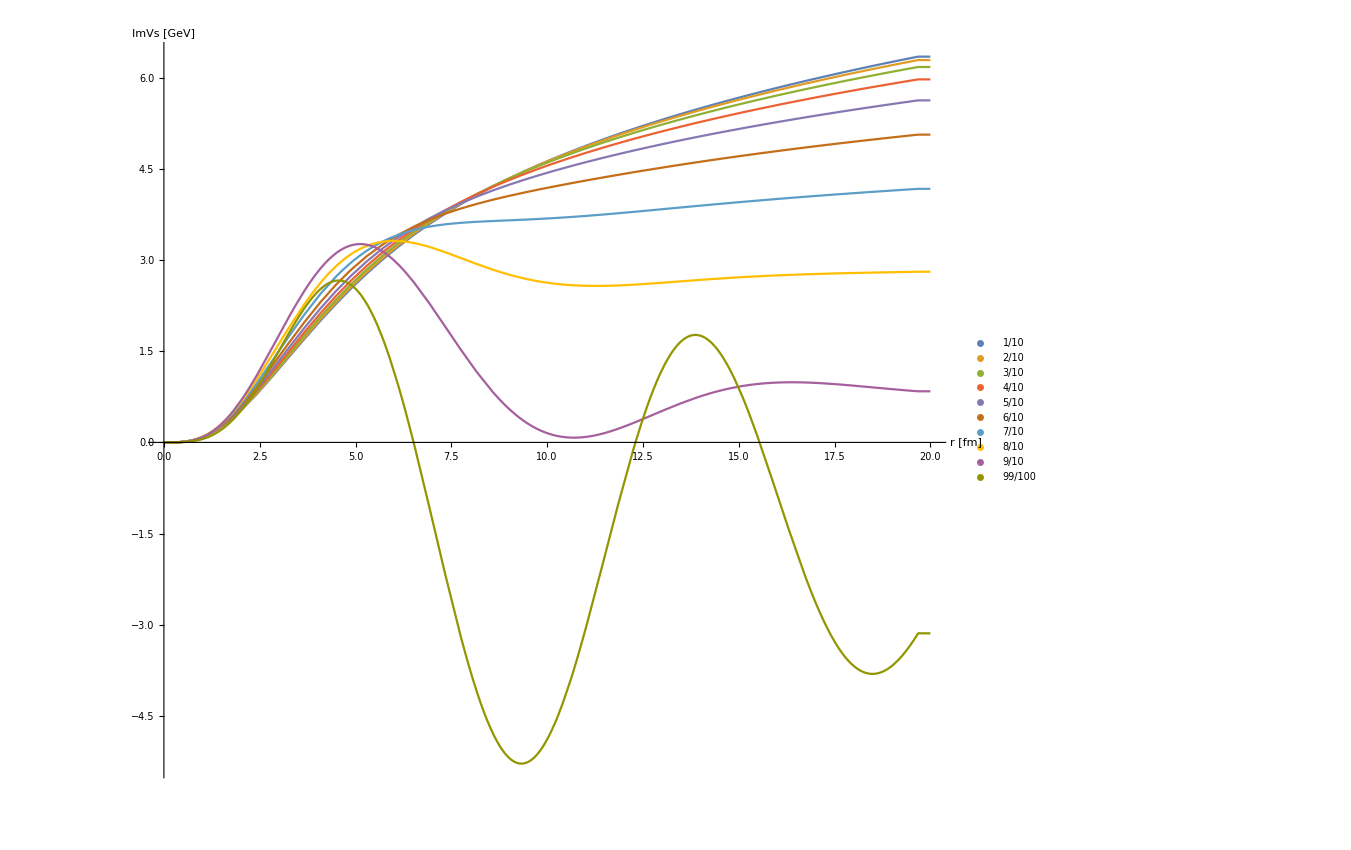

```mathematica
Plot[{Re[ImVsu[1][r/0.197]],Re[ImVsu[2][r/0.197]],Re[ImVsu[3][r/0.197]],Re[ImVsu[4][r/0.197]],Re[ImVsu[5][r/0.197]],Re[ImVsu[6][r/0.197]],Re[ImVsu[7][r/0.197]],Re[ImVsu[8][r/0.197]],Re[ImVsu[9][r/0.197]],Re[ImVsu[10][r/0.197]]},{r,1/1000,20},AxesStyle->Directive[FontSize->25,Thickness->0.004,FontFamily->"Helvetica",Black],BaseStyle->{FontSize->14},AspectRatio->0.85,AxesLabel->{"r [fm]","ImVs [GeV]"},ImageSize->{1000,1000},PlotLegends->Placed[PointLegend[uSetS, LegendMarkerSize->25,LegendLayout->{"Row",3}],{0.8,0.3}],BaseStyle->{FontSize->14}]
```

## Spectra

### Modules

```mathematica
ParallelSow[expr_]:=Sow[expr];
SetSharedFunction[ParallelSow];
```

```mathematica
δ=1/100; 
dω=0.0002;
```

#### Charmonium s-wave

```mathematica
swaveccspectra[u_]:=Block[{α=αcont[[1]],c=ccont[[1]],M=Mc,l=0,ωmin=-1,ωmax=2,ccss,inf,ρtable,ω,rhow,gr0,s1,V},
V[r_]:=ReVsu[u][r]+ReVcu[u][r]+ⅈ(ImVsu[u][r]+ImVcu[u][r]);
ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["cc_perp/swccu"<>ToString[Round[10u]]<>"spectra.dat",Sort[ccss]];
];
```

```mathematica
swavebbspectra[u_]:=Block[{α=αcont[[1]],c=ccont[[1]],M=Mb,l=0,ωmin=-1,ωmax=3,ccss,inf,ρtable,ω,rhow,gr0,s1,V},
V[r_]:=ReVsu[u][r]+ReVcu[u][r]+ⅈ(ImVsu[u][r]+ImVcu[u][r]);
ρtable=ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf}];
rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ParallelSow[{ω+2M,rhow[inf]}],{it,1,(ωmax-ωmin)/(dω M)}]//Reap//Last//First;

ccss=ParallelTable[{ρtable[[i,1]],(-ρtable[[i,2]])/ρtable[[i,1]]^2},{i,1,Length[ρtable]}];
Export["bb_perp/swbbu"<>ToString[Round[10u]]<>"spectra.dat",Sort[ccss]];
];
```

```mathematica
swaveccspectra[10]
```

```mathematica
swavebbspectra[10]
```